# Diffie-Hellman Algorithm

Diffie-Hellman Algorithm is an algorithm of securely exchanging cryptographic keys in the modern internet to ensure the Transport Layer Security.

Siyi(Raymond) Guo, Jun. 24,  2018

Modern internet security involves the usage of RSA. In particular, we use a pair of Private and Public key to encrypt and decrypt the message. However, the disadvantage of RSA is that if one part lost its private key, all the past communication can be decrypted. Therefore we need to find a way that both parties can share the information, and past communication can still be protected if one party lost its private key. And this is the motivation for Diffie Hellman Algorithm, an algorithm that allow both parties to calculate a shared key without having to ever explicitly communicate the shared key.

## Section Header

The idea behind Diffie-Hellman is that, both party have a common tool, each of them adding its own secret to the tool that explicitly communicate the new message over the internet. And we can find a tricky way that both party can recover the received message with its own secret.

Here is a visualization of how the algorithm works.

```mathematica
SetDirectory[NotebookDirectory[]];
Import["illustration.png"]
```

-Graphics-

## A small example of application

To illustrate the algorithm, here is a example.

Alice and Bob Started with a common paint.

This is a pair of integers {g,p}. p is a prime, and g is a primitive root modulo p.  For now, just think primitive root modulo as a special connection between g and p such that made them a good friends.

```mathematica
g = 5;
p = 23;
```

Now Alice holding the private key a:

```mathematica
a = 4;
```

To generate the message that will be sent to Bob is g^a mod p:

```mathematica
AliceSecret= Mod[g^a, p]
```

4

And Bob has the private key b:

```mathematica
b = 3;
```

The generated message that Bob will send to Alice is g^b mod p:

```mathematica
BobSecret = Mod[g^b, p]
```

10

Now Alice and Bob will sent g, p, AliceSecretToBob(g^a mod p), BobSecretToAlice(g^b mod p) to each other in PLAIN TEXT.

Alice to Bob:

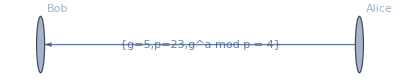

```mathematica
Graph[{Labeled["Alice"->"Bob",{"g=5","p=23", "g^a mod p = 4"}]}, VertexLabels->"Name"]
```

Bob to Alice:

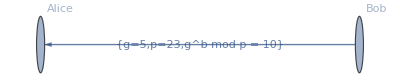

```mathematica
Graph[{Labeled["Bob"->"Alice",{"g=5","p=23", "g^b mod p = 10"}]}, VertexLabels->"Name"]
```

After the Communication, now Alice has g, p, a(Alice’s private key) and BobSecrect:

```mathematica
{"g"->g, "p"->p, "a"->a,"BobSecret"->BobSecret}
```

{g→5,p→23,a→4,BobSecret→10}

We can then calculate the Common Secret: BobSecret^a mod p

```mathematica
AliceReceivedCommonSecret = Mod[BobSecret^a , p]
```

18

So how about Bob? he now has g, p, b(Bob’s private Key), and AliceSecret:

```mathematica
{"g"->g, "p"->p, "b"->b,"AliceSecret"->AliceSecret}
```

{g→5,p→23,b→3,AliceSecret→4}

We can therefore Calculate the Common Secret: AliceSecret^b mod p

```mathematica
BobReceivedCommonSecret = Mod[AliceSecret^b, p]
```

18

We can find What Alice Decoded equal to What Bob Decoded, and therefore, this number become their Common Secret.

```mathematica
AliceReceivedCommonSecret == BobReceivedCommonSecret
```

True

And this Common Secret can be used as a key for the Symmetric Encryption to transfer the information, without the concern of key being exposed at the beginning of the Communication.

## The Mathematical induction

Here is a formula proof of how Alice and Bob end up with the same Result

Alice And Bob have:

```mathematica
ClearAll[g,p,a,b];
"Alice"->{"Common Pair"->{g,p}, "PrivateKey"->a}
"Bob" ->{"Common Pair"->{g,p}, "PrivateKey"->b}
```

Alice→{Common Pair→{g,p},PrivateKey→a}

Bob→{Common Pair→{g,p},PrivateKey→b}

Alice and Bob Encrypt Message:

```mathematica
A=Mod[g^a,p]
B=Mod[g^b, p]
```

Mod[g^a,p]

Mod[g^b,p]

But in fact, when Alice use B^a mod p and Alice use A^b mod p to decrypt is basically doing:

Alice

```mathematica
Mod[B^a, p] == Mod[g^(ab), p] == Mod[g^(ba), p] == Mod[A^b, p];
```

## Why it is secure?

Primitive root modulo

-Graphics-

## Author contact information

guosiyi1997@outook.com

(We recommend using your wolfram ID, but any address where you would like to be contacted about this publication should work.)

## Guidelines for the Author

### Image

Try to use images created in the Wolfram Language as much as possible

If an external image is the only way to go, use Import to get the image into the notebook and reverse close the In/Out cell-group  to hide the input cell.

### Text

Use minimal text in small pieces to explain the topic and transition between pieces of code. One or two lines of text at a time should suffice.

Sub-guideline two

### CodeText

Before each line of code, add a single line in CodeText style, as a lead-in, to say what the code that follows will do.

End this line with a colon

Make a map of Monaco:

```mathematica
GeoGraphics[Entity["Country","Monaco"]]
```

-Graphics-

### Code

Keep code simple and straightforward; code cell should be at most 3 lines long

Breakup complicated lengthy code into multiple segments and separate with CodeText lead-ins explaining each segment

Try to create simple visualizations whenever possible to illustrate the topic and add visual interest

Extra code (for example, visualization options to simply make the output look pretty) can be distracting and take away focus from the main functionality. Either avoid these or use Iconize to hide them.

Instead of

```mathematica
Plot[Sin[x], {x, 1, 10}, PlotStyle -> {Red, Dashed, Thick}]
```

Use

```mathematica
Plot[Sin[x],{x,1,10},]
```

If using a Manipulate, remember to set SaveDefinitions->True, if it refers to definitions not contained within it. This will allow the Manipulate to work without having to re-evaluate the notebook, for every new session.

Include Data Repository

Include Function Repository (mention coming soon)